```mathematica
allGraphs4[K4Key,"parents"]
```

{363,361,355,337,283,121}

```mathematica
allGraphs4[361,"colofourrealnull"]
```

-4 n1234+2 n123x4+n124x3+n12x34-n12x3x4+2 n134x2-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4

```mathematica
ChangeSymbol[s_]:=Symbol[StringReplace[SymbolName[s],"v"->"n"]]
```

```mathematica
SetDifference[full_,small_]:=Select[full,!MemberQ[small,#]&]
```

```mathematica
Map[ChangeSymbol[#]&,allGraphs4[361,"colofour"]]
```

n1x24x3+n1x2x3x4

```mathematica
Descendents[g_,vertices_]:=Block[{result={},nodes,edges,current},
nodes=vertices;
While[nodes≠{},
current=First[nodes];
nodes=Rest[nodes];
edges=Select[EdgeList[g],#[[1]]==current&];
result=Join[result,edges];
nodes=Join[nodes,Map[#[[2]]&,edges]];
];
result
]
```

```mathematica
CalcSubGraph[g_,inf_]:=Block[{involved={}, current={inf},result={}, values},
result={inf};
current=Map[#[[1]]&,Select[EdgeList[g],MemberQ[current,#[[2]]]&]];
While[current≠{},
result=Join[result,current];
current=Map[#[[1]]&,Select[EdgeList[g],MemberQ[current,#[[2]]]&]];
];
result=Sort[DeleteDuplicates[result]];
values=Select[Keys[allGraphs4],Sort[ListofVars[allGraphs4[#,"colofourrealnull"]]]==result&];
If[Length[values]>1,
Print[values];
Interrupt[]
];
First[values]
]
```

```mathematica
allGraphs4[CalcSubGraph[allGraphs4[40,"graph"],n134x2],"graph"]
```

-Graphics-

```mathematica
Select[Keys[allGraphs4],Length[Intersection[ListofVars[allGraphs4[#,"colofourrealnull"]],{n12x34,n12x3x4,n1x2x34,n1x2x3x4}]]==4&]
```

{364,361,355,352,337,334,328,325,283,280,274,271,256,253,247,244}

```mathematica
allGraphs4[244,"graph"]
```

-Graphics-

```mathematica
SummaryPrint[40]
```

SummaryPrint[40]

```mathematica
MobiusGraphDouble[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs4[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,edgesTrans, bondGraphs, sublattice},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=Descendents[Graph[vars,edges],nonRoot];
sublattice=mob;
bondGraphs=Association[Map[#->allGraphs4[ CalcSubGraph[sublattice,#],"graph"]&,VertexList[sublattice]]];
Graph[vars,edges,VertexLabels->Table[n->Placed[Tooltip[
TableForm[
With [{baseList=
{
Style[n,12,"Calibri",If[Coefficient[form3,n]==0,Black,Blue]],
Style[Coefficient[form2,n],Bold,If[Coefficient[form2,n]==0,Blue,Red]]
}},
If[KeyExistsQ[bondGraphs,n],
Join[baseList,{Framed[bondGraphs[n],Background->Transparent]}],
baseList
]
],TableAlignments->Center],
TableForm[
{found[n,"graph"],bondGraphs[n]}]],{Left}
],{n,vars}],GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Join[
Map[#->{Thick,Darker[Green]}&,Select[edgesTrans,!MemberQ[edges2,#]&&!MemberQ[EdgeList[mob],#]&]],
Map[#->{Thick,Blue}&,edges2]
],
GraphHighlight->Join[VertexList[mob],EdgeList[mob]],
GraphHighlightStyle->"Thick",
ImageSize->720]
]
```

```mathematica
allGraphs4[0,"signature"]
```

0

```mathematica
allGraphs4AtomKeysFakeNull=Select[Keys[allGraphs4],Length[ListofVars[allGraphs4[#,"colofournull"]]]==1&];Length[allGraphs4AtomKeysFakeNull]
```

15

```mathematica
repBase4Bis=Table[allGraphs4[k,"colofournull"]->Labeled[Graph[allGraphs4[k,"graph"]],Style[allGraphs4[k,"colofournull"],Blue,12],ImageSize->{50,50}],{k,allGraphs4AtomKeysFakeNull}]
```

{p1x2x3x4→-Graphics-p1x2x3x4,p12x3x4→-Graphics-p12x3x4,p1234→-Graphics-p1234,p123x4→-Graphics-p123x4,p124x3→-Graphics-p124x3,p12x34→-Graphics-p12x34,p13x2x4→-Graphics-p13x2x4,p134x2→-Graphics-p134x2,p13x24→-Graphics-p13x24,p14x2x3→-Graphics-p14x2x3,p14x23→-Graphics-p14x23,p1x23x4→-Graphics-p1x23x4,p1x234→-Graphics-p1x234,p1x24x3→-Graphics-p1x24x3,p1x2x34→-Graphics-p1x2x34}

```mathematica
repBase4=Table[allGraphs4[k,"colofour"]->Labeled[Graph[allGraphs4[k,"graph"]],Style[allGraphs4[k,"colofour"],Blue,12],ImageSize->{50,50}],{k,allGraphs4AtomKeys}]
```

{v1x2x3x4→-Graphics-v1x2x3x4,v1x2x34→-Graphics-v1x2x34,v1x24x3→-Graphics-v1x24x3,v1x23x4→-Graphics-v1x23x4,v1x234→-Graphics-v1x234,v14x2x3→-Graphics-v14x2x3,v14x23→-Graphics-v14x23,v13x2x4→-Graphics-v13x2x4,v13x24→-Graphics-v13x24,v134x2→-Graphics-v134x2,v12x3x4→-Graphics-v12x3x4,v12x34→-Graphics-v12x34,v124x3→-Graphics-v124x3,v123x4→-Graphics-v123x4,v1234→-Graphics-v1234}

```mathematica
repBase4
```

{v1x2x3x4→-Graphics-v1x2x3x4,v1x2x34→-Graphics-v1x2x34,v1x24x3→-Graphics-v1x24x3,v1x23x4→-Graphics-v1x23x4,v1x234→-Graphics-v1x234,v14x2x3→-Graphics-v14x2x3,v14x23→-Graphics-v14x23,v13x2x4→-Graphics-v13x2x4,v13x24→-Graphics-v13x24,v134x2→-Graphics-v134x2,v12x3x4→-Graphics-v12x3x4,v12x34→-Graphics-v12x34,v124x3→-Graphics-v124x3,v123x4→-Graphics-v123x4,v1234→-Graphics-v1234}

```mathematica
SummaryPrint[k_]:=With[
{g=MobiusGraphDouble[K4Key,k,allGraphs4], gr=allGraphs4[k,"graph"]},
Framed[
Labeled[
Row[{
Labeled[Graph[gr,ImageSize->{40,40}],Style[k,Bold,12, Underlined,Red]],
Rotate[g,Pi/2]
}],
{Style[StandardForm[allGraphs4[k,"colofourrealnull"]],Darker[Green],12],
Column[
{Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],Row[Table[Style[ChromaticPolynomial[gr,m],Blue],{m,1,5}], " * "],
Framed[Style[StandardForm[((allGraphs4[k,"colofour"])/.repBase4)],Darker[Green],12]]},
Center
]
},
{Top,Bottom,Bottom}
]
]
]
```

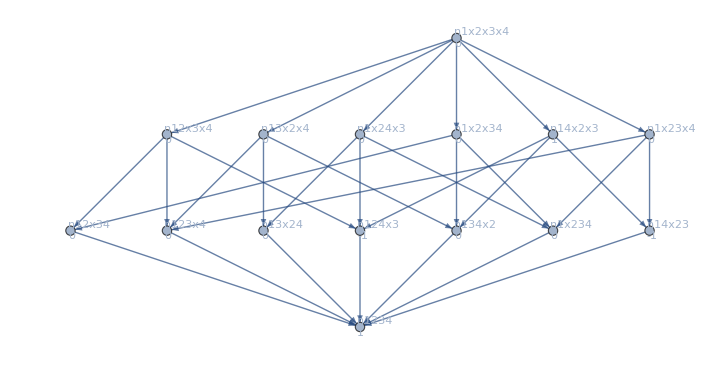
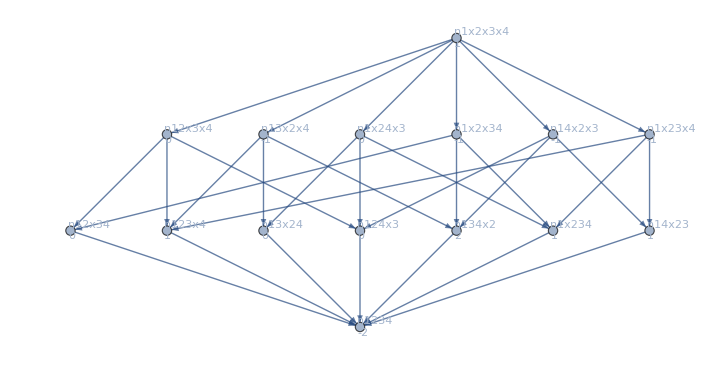
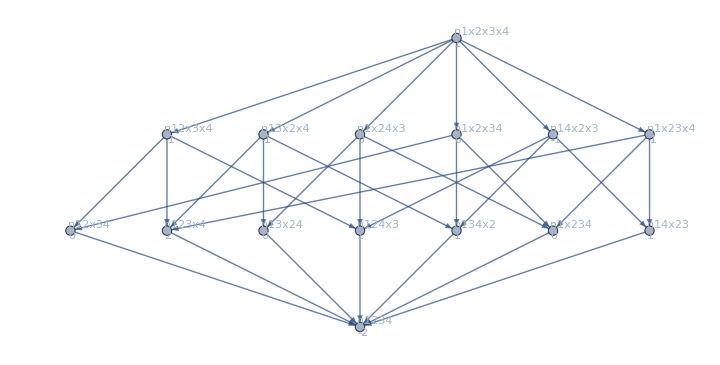
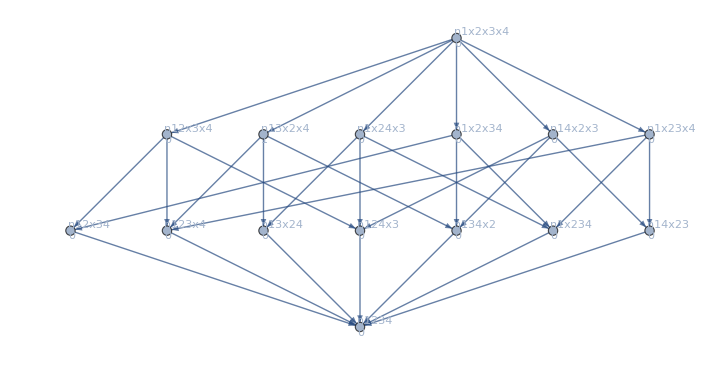
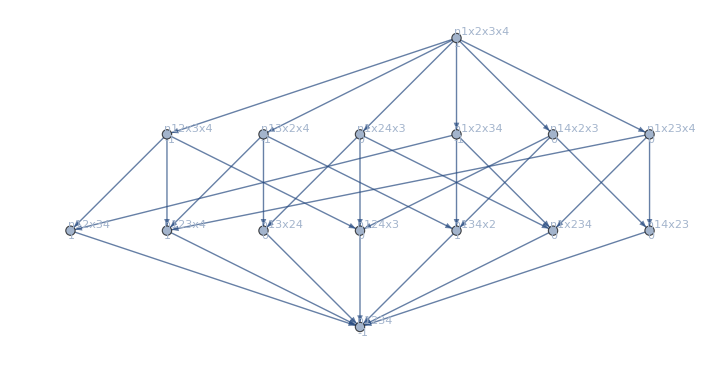
{-Graphics-309-Graphics-n1234-n124x3-n14x23+n14x2x3x^3-2 x^2+x
(x-1)^2 x
 *  * 02123680
-Graphics-v134x2+-Graphics-v14x2x3,-Graphics-118-Graphics--2 n1234+n123x4+2 n134x2-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4x^4-4 x^3+5 x^2-2 x
(x-2) (x-1)^2 x
 *  * 001272240
-Graphics-v12x3x4+-Graphics-v1x24x3+-Graphics-v1x2x3x4,-Graphics-360-Graphics--2 n1234+2 n123x4+n124x3-n12x3x4+n134x2-n13x2x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4x^4-4 x^3+5 x^2-2 x
(x-2) (x-1)^2 x
 *  * 001272240
-Graphics-v1x24x3+-Graphics-v1x2x34+-Graphics-v1x2x3x4,-Graphics-162-Graphics-n13x2x4x^3
x^3
 *  * 182764125
-Graphics-v1234+-Graphics-v123x4+-Graphics-v134x2+-Graphics-v13x24+-Graphics-v13x2x4,-Graphics-325-Graphics--n1234+n123x4+n12x34-n12x3x4+n134x2-n13x2x4-n1x2x34+n1x2x3x4x^4-3 x^3+3 x^2-x
(x-1)^3 x
 *  * 0224108320
-Graphics-v14x23+-Graphics-v1x23x4+-Graphics-v14x2x3+-Graphics-v1x24x3+-Graphics-v1x2x3x4}

```mathematica
Table[
SummaryPrint[k]
,{k,RandomSample[ Keys[allGraphs4],5]}
]
```